## Kapitola 9 - Shlukování dat sítí bez učitele

Demonstrace použití neuronové sítě bez učitele k hledání shluků v datech.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Vytvoření trénovacích dat

Vygenerujeme si data, na kterých budeme prezentovat shlukování. Protože pracujeme se sítí bez učitele, postačí nám vstupní data a nepotřebujeme generovat žádná výstupní data.

```mathematica
values=10;
cluster1x =RandomReal[{-0.1,0.1},{values,1}];cluster1y=RandomReal[ {-0.1,0.1},{values,1}];
cluster2x =RandomReal[{-0.1,0.1},{values,1}];cluster2y=RandomReal[ {0.9,1.1},{values,1}];
cluster3x =RandomReal[{0.3,0.5},{values,1}];cluster3y=RandomReal[ {1.4,1.6},{values,1}];
cluster4x =RandomReal[{0.9,1.1},{values,1}];cluster4y=RandomReal[ {2.1,1.9},{values,1}];
cluster5x =RandomReal[{1.4,1.6},{values,1}];cluster5y=RandomReal[ {1.4,1.6},{values,1}];
cluster6x =RandomReal[{1.9,2.1},{values,1}];cluster6y=RandomReal[ {1.1,0.9},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inData= Join[cluster1,cluster2,cluster3,cluster4,cluster5,cluster6];
```

Vygenerovaná data jsou dvoudimenzionální a obsahují 6 jasně oddělených shluků.

Data si můžeme zobrazit zde.

```mathematica
inData
```

{{-0.00223458,-0.0288234},{-0.0822471,0.0884684},{-0.0204159,-0.0533084},{-0.0707947,-0.0861079},{0.0249019,-0.0129785},{0.00522467,-0.0381483},{0.0448618,0.0823795},{0.0827508,0.068222},{0.0983657,-0.0244083},{0.0804644,0.0167135},{0.0313767,1.07553},{-0.0017817,0.94603},{-0.0554051,1.01124},{0.0844582,0.940195},{0.0197356,1.02034},{-0.064047,1.02663},{0.00232464,0.925151},{0.0359133,0.909784},{-0.0020023,1.07839},{-0.00568624,1.01497},{0.388465,1.42201},{0.387323,1.50616},{0.354026,1.47833},{0.436685,1.47837},{0.497604,1.45834},{0.421821,1.57962},{0.356176,1.51757},{0.358353,1.40382},{0.333832,1.47531},{0.326097,1.46661},{1.02171,2.06764},{1.0795,2.09162},{0.941659,2.04755},{0.916947,2.07916},{1.07591,2.06814},{0.906284,2.02133},{1.03429,1.93847},{1.06006,1.92238},{1.07499,1.97797},{0.994674,2.09158},{1.59658,1.4662},{1.42147,1.56766},{1.51399,1.55679},{1.43189,1.58064},{1.4836,1.44911},{1.49595,1.50753},{1.53102,1.52273},{1.42641,1.46726},{1.47657,1.455},{1.49363,1.40614},{1.96374,0.944373},{2.0407,0.963575},{2.04918,1.02273},{2.03996,1.02978},{1.98175,1.0213},{2.03972,0.990023},{2.08157,1.02026},{1.96731,0.955967},{1.9532,0.994229},{1.9968,0.95978}}

Pro lepší představu o struktuře dat si je můžeme zobrazit v grafu.

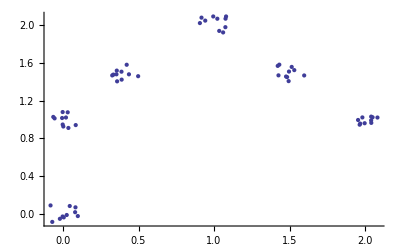

```mathematica
ListPlot[inData]
```

## Zpracování dat neuronovou sítí

### Náhodně inicializovaná síť

Nejprve vytvoříme neuronovou síť o šesti neuronech. Počet neuronů určuje kolik shluků se síť pokusí v datech najít.

```mathematica
unsup=InitializeUnsupervisedNet[inData,6];
```

Tuto neuronovou síť naučíme na našich datech

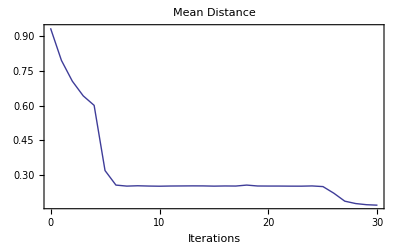

UnsupervisedNet::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{unsup,fitrecord}=UnsupervisedNetFit[inData,unsup,30,ReportFrequency->1];
```

Vidíme že během učení sítě jeden z neuronů “zemřel”, tzn. není použit k rozlišení shluků v datech. Později se mu ještě budeme věnovat.

Ilustraci jaým způsobem byla data rozdělena do shluků nám poskytne následující graf. Pozice neuronu, který reprezentuje daný shluk je naznačena tučným číslem. Je také jasně vidět, který neuron je “mrtvý” a nepřináší nám žádný užitek.

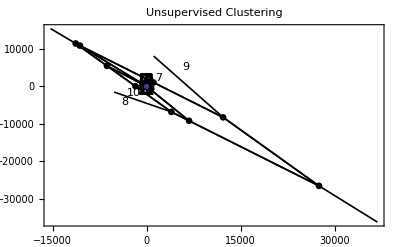

```mathematica
NetPlot[unsup,inData,CbvSymbol->{FontSize->30}]
```

Můžeme také jednoduše nechat “oklasifikovat” nový vektor (zadáme jeho x a y souřadnici).

```mathematica
unsup[{0.2,0.7}]
```

{1}

Číslo, které nám síť vrátila znamená číselné označení shluku, kam vektor spadá (odpovídá číslům v grafu)

Nyní si vzpomeneme, že máme v síti nepotřebný neuron, budeme ho tedy chtít odstranit.
Nejdříve zjistíme o který neuron se jedná.

```mathematica
UnUsedNeurons[unsup,inData]
```

{3}

A poté ho odstraníme. Novou síť bez nepotřebného neuronu pojmenujeme unsup1.

```mathematica
unsup1=NeuronDelete[unsup,%]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2011, 4, 19, 22, 35, 30.6634746}, AccumulatedIterations → 30, SOM → None}]

Podíváme se jakým způsobem odděluje síť jednotlivé shluky po odebrání nepotřebného neuronu.

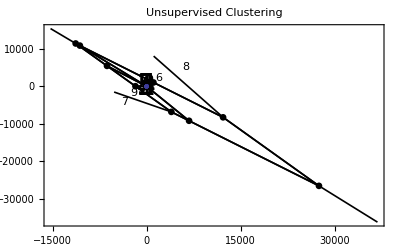

```mathematica
NetPlot[unsup1,inData,CbvSymbol->{FontSize->30}]
```

### Síť inicializovaná metodou SOM

Protože vidíme, že rozdělení dat na shluky ještě není perfektní můžeme se pokust dosáhnout ještě lepšího rozdělení. Místo náhodné inicializace sítě můžeme použít SOM (samoorganizující mapu) k inicializaci sítě. Samoorganizující mapa se nechá přizpůsobit datům, na souřadnicích, kde skončí její neurony, jsou inicializovány neurony naší požadované sítě (naše síť není SOM).

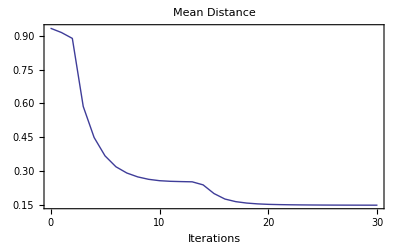

```mathematica
unsup2=InitializeUnsupervisedNet[inData,6,UseSOM ->True,CriterionPlot->True,CriterionLog->True,Iterations->30];
```

Nyní naučíme zinicializovanou síť na našich datech.

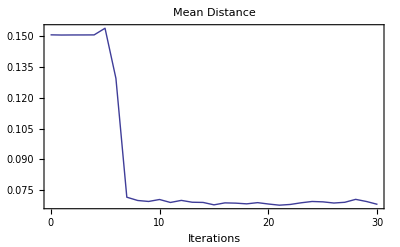

```mathematica
{unsup2,fitrecord2}=UnsupervisedNetFit[inData,unsup2,30];
```

A podíváme se jakým způsobem uřčuje shluky v datech.

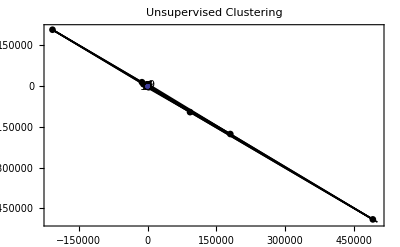

```mathematica
NetPlot[unsup2,inData]
```

Tento přístup k inicializaci sítě nám může často pomoci dosáhnout lepších výsledků, než náhodná inicializace. Také často zabrání problému s “mrtvými” neurony.

## Průběh učení

### Náhodně inicializovaná síť

Ještě se můžeme podívat jak síť v průběhu učení dělila data do shluků a jak se měnila poloha jednotlivých neuronů. Barevné čáry ukazují pohyb jednotlivých neuronů, čísla ukazují jejich konečnou polohu.

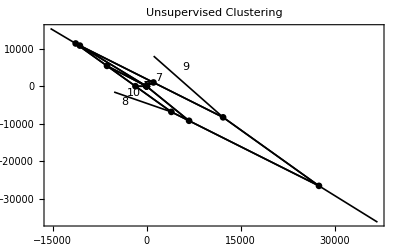

```mathematica
NetPlot[fitrecord,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState=NetPlot[fitrecord,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

### Síť inicializovaná metodou SOM

Z následujícího grafu je patrné, že i pouze zinicializovaná síť metodou SOM by poskytovala poměrně dobré výsledky a její učení upravuje pouze pozici několika neuronů.

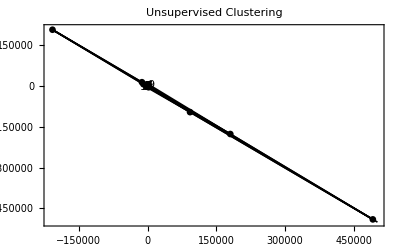

```mathematica
NetPlot[fitrecord2,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích. Pro správnou funkci je třeba mít vyhodnocené všechny výše se nacházející buňky.

```mathematica
learningState2=NetPlot[fitrecord2,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState2[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.